```mathematica
AbsdeltaD[Ne_]:=Abs[Simplify[ReplaceAll[Simplify[Limit[(3 ((1+q)^l (-1+l^2-3 l q+3 q^2)-(-1+q)^l (-1+l^2+3 l q+3 q^2)))/((-1+l) ((1+l-q) (1+q)^(1+l)+(-1+q)^(1+l) (1+l+q))),l->3/4]],q->100*Exp[2*Ne]]]]
```

```mathematica
Limit[AbsdeltaD[Ne],Ne->Infinity]
```

0

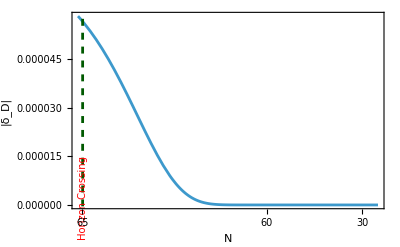

```mathematica
pp=Quiet[Plot[N[Evaluate@AbsdeltaD[Ne],100],{Ne,0,65},ScalingFunctions->{"Log","Linear"},Frame->True,WorkingPrecision->1000,AccuracyGoal->80,PrecisionGoal->80,PlotRange->{{0,65},{"None",0.00006}},(*1. Relabel the tick numbers on the bottom axis*)FrameTicks->{{Automatic,Automatic},{{{0.07,"65"},{1,"64"},{5,"60"},{25,"50"},{45,"30"},{65,"0"}},Automatic}},(*2. Relabel the axis title*)FrameLabel->{{"|\!\(\*SubscriptBox[\(δ\), \(D\)]\)|",None},{"N",None}},(*3. Add the Horizon Crossing line and label*)Epilog->{DarkGreen,Dashed,Thickness[0.005],InfiniteLine[{-2.65,0},{-2.65,1}],(*CHANGE 10^-3 TO A Y-VALUE NEAR THE TOP OF YOUR PLOT*)Text[Style["   Horizon Crossing   ",10,Red,Background->White],{-2.65,0.000002},{-1.1,0},{0,1}]}]]
```

```mathematica
SetDirectory[NotebookDirectory[]];Export["delta_D.pdf",pp,ImageResolution->300];
```